0

1

2

3

4

5

6

7

8

9

10

11

12

20.8279

1/2 √(3/π) Cos[θ]+1/2 √(5/π) (-1+3 Cos[θ]^2)+3/4 √(7/π) (-3 Cos[θ]+5 Cos[θ]^3)+(3 (3-30 Cos[θ]^2+35 Cos[θ]^4))/(4 √π)+5/16 √(11/π) (15 Cos[θ]-70 Cos[θ]^3+63 Cos[θ]^5)+3/16 √(13/π) (-5+105 Cos[θ]^2-315 Cos[θ]^4+231 Cos[θ]^6)+7/32 √(15/π) (-35 Cos[θ]+315 Cos[θ]^3-693 Cos[θ]^5+429 Cos[θ]^7)+1/32 √(17/π) (35-1260 Cos[θ]^2+6930 Cos[θ]^4-12012 Cos[θ]^6+6435 Cos[θ]^8)+9/256 √(19/π) (315 Cos[θ]-4620 Cos[θ]^3+18018 Cos[θ]^5-25740 Cos[θ]^7+12155 Cos[θ]^9)+5/256 √(21/π) (-63+3465 Cos[θ]^2-30030 Cos[θ]^4+90090 Cos[θ]^6-109395 Cos[θ]^8+46189 Cos[θ]^10)+11/512 √(23/π) (-693 Cos[θ]+15015 Cos[θ]^3-90090 Cos[θ]^5+218790 Cos[θ]^7-230945 Cos[θ]^9+88179 Cos[θ]^11)+(15 (231-18018 Cos[θ]^2+225225 Cos[θ]^4-1021020 Cos[θ]^6+2078505 Cos[θ]^8-1939938 Cos[θ]^10+676039 Cos[θ]^12))/(512 √π)

-Graphics3D-

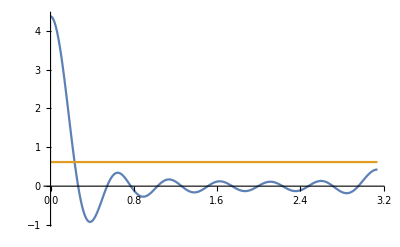

```mathematica
m1Y00=0
m1Y01=1
m1Y02=2
m1Y03=3
m1Y04=4
m1Y05=5
m1Y06=6
m1Y07=7
m1Y08=8
m1Y09=9
m1Y010=10
m1Y011=11
m1Y012=12
NConst =20.827948231018638
m1[x_]=m1Y00*SphericalHarmonicY[0,0,θ,0]+m1Y01*SphericalHarmonicY[1,0,θ,0]+m1Y02*SphericalHarmonicY[2,0,θ,0]+m1Y03*SphericalHarmonicY[3,0,θ,0]+m1Y04*SphericalHarmonicY[4,0,θ,0]+m1Y05*SphericalHarmonicY[5,0,θ,0]+m1Y06*SphericalHarmonicY[6,0,θ,0]+m1Y07*SphericalHarmonicY[7,0,θ,0]+m1Y08*SphericalHarmonicY[8,0,θ,0]+m1Y09*SphericalHarmonicY[9,0,θ,0]+
m1Y010*SphericalHarmonicY[10,0,θ,0]+m1Y011*SphericalHarmonicY[11,0,θ,0]+m1Y012*SphericalHarmonicY[12,0,θ,0]

SphericalPlot3D[{(1/NConst)*m1[θ], (3/(4 Pi))^(1/3)},{θ,0,π},{ϕ,0,π}, PlotRange -> All]
Plot[{(1/NConst)*m1[θ], (3/(4 Pi))^(1/3)},{θ,0,π}, PlotRange -> All]
```

```mathematica
Show[%724,ViewPoint->{0,-∞,0}]
```

```mathematica
SphericalPlot3D[{ (1/NConst)*SphericalHarmonicY[0,0,θ,ϕ]+(2/NConst)*SphericalHarmonicY[1,0,θ,ϕ] , (3/(4 Pi))^(1/3) },{θ,0,Pi},{ϕ,0,Pi}, PlotRange -> All]
```

-Graphics3D-

```mathematica
SphericalPlot3D[{ (2/NConst)*SphericalHarmonicY[1,0,θ,ϕ] , (3/(4 Pi))^(1/3) },{θ,0,Pi},{ϕ,0,Pi/2}, PlotRange -> All]
```

-Graphics3D-

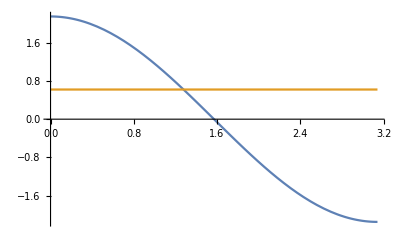

```mathematica
Plot[{(2/NConst)*SphericalHarmonicY[1,0,θ,0] , (3/(4 Pi))^(1/3) },{θ,0,Pi}, PlotRange -> All]
```

```mathematica
N[Integrate[Sin[θ]((m1[x_]/NConst)^3 )/ 3, {θ,0,Pi},{ϕ,0,2 Pi}]]
```

1.

```mathematica
(9035.235330699883)^(1/3)
```

20.8279

```mathematica
N[Integrate[Sin[θ](((1/NConst)*SphericalHarmonicY[0,0,θ,ϕ]+(1/NConst)*SphericalHarmonicY[1,0,θ,ϕ]+(2/NConst)*SphericalHarmonicY[2,0,θ,ϕ])^3 )/ 3, {θ,0,Pi},{ϕ,0,2 Pi}]]
```

26.4775

```mathematica
N[Integrate[Sin[θ]((SphericalHarmonicY[1,0,θ,ϕ])^3 )/ 3, {θ,0,Pi},{ϕ,0,2 Pi}]]
```

0.

```mathematica
Simplify[Integrate[Sin[θ]((3/ (4 Pi))^(1/3))^3 / 3, {θ,0,Pi},{ϕ,0,2 Pi}]]
```

1

```mathematica
1/3.4797502354857413*^-7
```

```mathematica
SphericalHarmonicY[12,0,θ,ϕ]
```

(5 (231-18018 Cos[θ]^2+225225 Cos[θ]^4-1021020 Cos[θ]^6+2078505 Cos[θ]^8-1939938 Cos[θ]^10+676039 Cos[θ]^12))/(2048 √π)

```mathematica
Expand[ (1-i+ 2)^3]
```

a^3+3 a^2 b+3 a b^2+b^3+6 a^2 c+12 a b c+6 b^2 c+12 a c^2+12 b c^2+8 c^3

```mathematica
Expand[((I+1)/Sqrt[2])^2]
```

ⅈ

```mathematica
Expand[((I+2)I)^2]
```

-3-4 ⅈ